## Basics of Mathematica

## Graphics

This section will cover the basic plots of simple algebraic and trigonometric functions in two dimensions and three dimensions.

### Basic Graphs in One Dimension

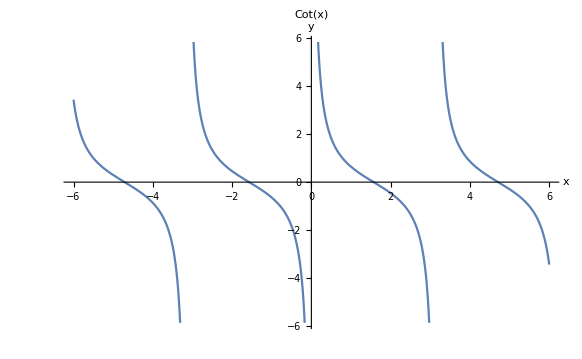

```mathematica
Plot[Cot[x],{x,-6,6},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold}, PlotLabel->"Cot(x)"]
```

#### The Function of a Simple Integral

```mathematica
Clear[x,t]
```

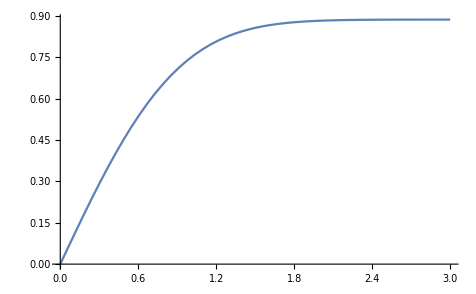

```mathematica
f[x_]:= Integrate[E^(-t^2),{t,0,x}]
Plot[f[x],{x,0,3}]
```

#### A collection of different functions within a single plot

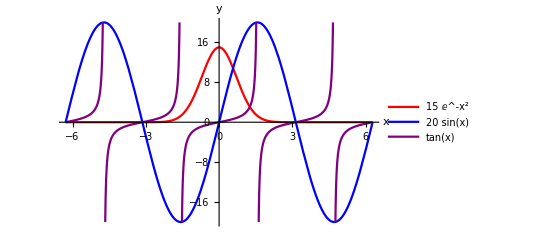

```mathematica
Plot[{15 E^(-x^2),20 Sin[x], Tan[x]},{x, -2 Pi, 2 Pi},PlotRange->{-20,20},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{"Times New Roman", 12, GrayLevel[0],Bold},PlotStyle->{Red, Blue, Purple},PlotLegends->"Expressions"]
```

### Parametric Plots

In this example we will plot two half circles. Using ParametricPlot function.

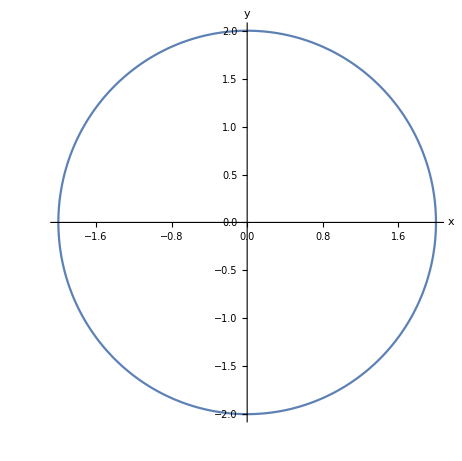

```mathematica
ParametricPlot[{2 Cos[t], 2 Sin[t]},{t,0,2 Pi},AspectRatio-> Automatic,AxesLabel ->{HoldForm[x],HoldForm[y]},PlotLegends->"Expressions"]
```

#### 4 Leaved Clover Graph

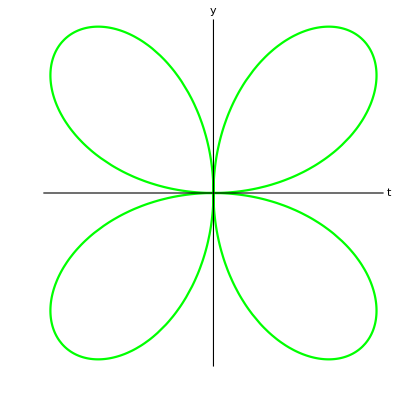

```mathematica
ParametricPlot[{Cos[t]Sin[2 t],Sin[t]Sin[2 t]},{t,0, 2Pi},AxesLabel ->{HoldForm[t],HoldForm[y]}, PlotStyle->Green,Ticks->None]
```

#### 5 Leaved Clover Graph

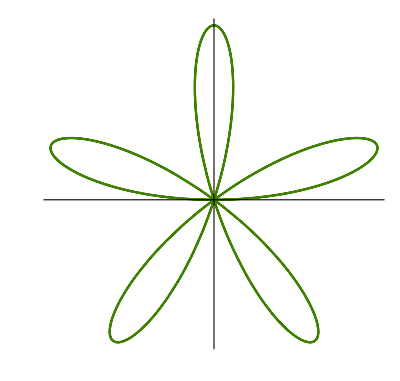

```mathematica
ParametricPlot[{Cos[t] Sin[5 t],Sin[t] Sin[5 t]},{t,0,2 Pi},PlotStyle->RGBColor[0.25098, 0.501946, 0.00895705],Ticks->None]
```

```mathematica
20 Leaved Clover Graph
```

20 Clover Graph Leaved

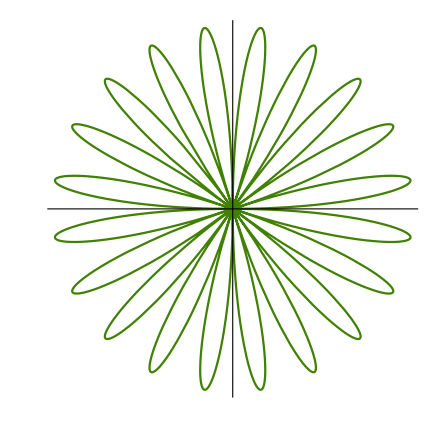

```mathematica
ParametricPlot[{Cos[t] Sin[10 t],Sin[t] Sin[10 t]},{t,0,2 Pi},PlotStyle->RGBColor[0.25098, 0.501946, 0.00895705],Ticks->None]
```

#### Contour and Density Plots

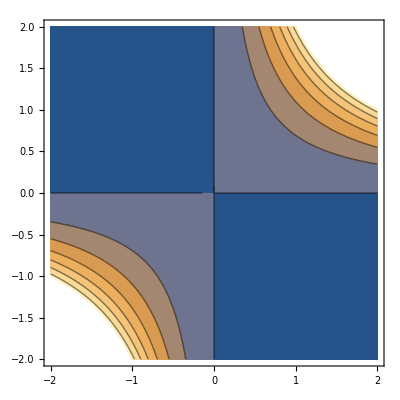

```mathematica
ContourPlot[E^(x y),{x,-2,2},{y,-2,2}]
```

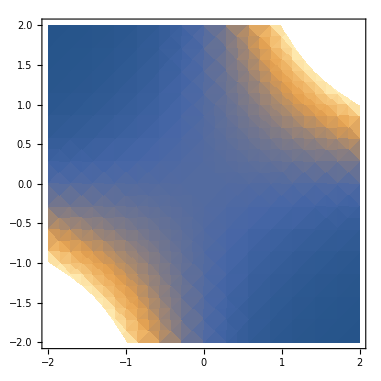

```mathematica
DensityPlot[E^(x y),{x,-2,2},{y,-2,2}]
```

### Basic Graphs in Three Dimensions

```mathematica
Plot3D[Cot[t u],{t,-3,3},{u,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Cot[t  u],{t,-3,3},{u,-3,3},PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
Plot3D[Cot[t u],{t,-6, 6},{u, -6, 6}, PlotTheme->"Classic"]
```

-Graphics3D-

#### Helix

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/5},{t,0,6 Pi}]
```

-Graphics3D-

```mathematica
Clear[u]
```

```mathematica
ParametricPlot3D[{Sin[t] Cos[u], Sin[t] Sin[u],Cos[t]},{t, 0, Pi},{u, 0, 2 Pi},PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{2 Cos[t] Cos[2t],2 Sin[t] Cos[2t],u},{t,0,Pi},{u,0,5},PlotTheme->"Business"]
```

-Graphics3D-